```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

```mathematica
drho[rho_,rho0_,drho2_]:=1/2(drho2-0.1)Tanh[rho-rho0]
```

```mathematica
CriticalAdaptive[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=Tabl;
ρinf=Round[consts[[2]]];
nn=Round[ρinf/dρ];
H=SparseArray[{{n_,n_}->2./dρ[[n]]^2-2./(n*dρ)ⅇ^(-n*dρ/λ)+(l(l+1))/(n*dρ)^2,{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,vah},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]]; (*Again, lets you know it's working/progress*)
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]), (*if there is a zero on the lower half*)
Return[Bisect[F,consts,x0,mid,ϵ]];, (*bisect it*)
Return[Bisect[F,consts,mid,xf,ϵ]]; (*otherwise try the upper half*)
];,
vah = F[xf,consts];
Return[{mid,lnegs,CountNegs[vah]}];
]
]
```

```mathematica
Findlc[input_,i_,eps_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[i]<>"th lambda, part "<>ToString[input[[1]]]];
res={input[[1]],Bisect[Critical,{input[[2,1]],input[[2,2]]},input[[3]],input[[4]],eps]};
Return[res]
]
```

```mathematica
l0data=Import["~/Thesis/Calculations/l0.csv"];
```

```mathematica
range={l0data[[4,1]]-3l0data[[4,2]],l0data[[4,1]]+3l0data[[4,2]]}
```

{12.6809,12.7017}

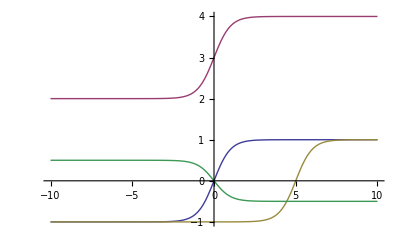

```mathematica
Plot[{Tanh[x],Tanh[x]+3,Tanh[x-5],-0.5Tanh[x]},{x,-10,10}]
```

```mathematica
drho[rho_,rho0_,drho2_]:=1/2(drho2-0.1)Tanh[rho-rho0]
```